```mathematica
ClearAll[r,rz,wzSolutions, ws, ws, w, z, a, b, c]
rz = Solve[(r-1)/r == (1/2)(z + 1/z), r];
(r-1)/r /. rz // FullSimplify // First
l2 =(r-2)/r /. rz // FullSimplify // First
l3 = (r-3)/r /. rz // FullSimplify // First

wzSolutions = NSolve[{4 l2^2 == 2 + w/z + z/w,4 l3^2 == 2 + w z + 1/(w z ), z Conjugate[z] == 1, w Conjugate[w] == 1,(1/2)(z + 1/z) ≠ 1, 1/(1 - (1/2)Re[z + 1/z]) > 3 }, {w, z}]
ws = (w /. wzSolutions) ;
zs = (z /. wzSolutions) ;

r[z_] := Re[1/(1-(1/2)(z + 1/z))]
a[z_, w_] := r[z] z
b[z_, w_] := r[z] w
c[z_, w_] := r[z] 1/z

r[#] &/@ zs
```

(1+z^2)/(2 z)

-1+1/z+z

-2+3/(2 z)+(3 z)/2

{{w→-0.961861-0.273539 ⅈ,z→0.742227-0.670148 ⅈ},{w→-0.961861+0.273539 ⅈ,z→0.742227+0.670148 ⅈ}}

{3.87939,3.87939}

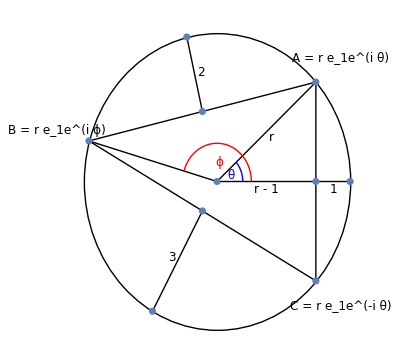

r | = | 3.87939
θ | = | 42.0785
ϕ | = | 164.125
area | = | 17.1866

```mathematica
ClearAll[z2v, cline, plotit, origin, fs]
origin = {0,0};
z2v[z_] := {z// Re, z//Im}
fs := Style[#, FontSize-> 12] &;
cline[z1_, z2_] := Line[ {z2v[z1], z2v[z2]}]
plotit[n_] := Module[{z,w,aa,bb,cc,rr,points, xx, yy, zz, xxr, yyr, zzr, th, ph},
z = zs[[n]];
w= ws[[n]];
aa = a[z,w];
bb = b[z,w];
cc = c[z,w];
xx = (aa + bb)/2;
yy = (bb + cc)/2;
zz = (cc + aa)/2;
rr = r[z];
xxr = rr xx/Abs[xx];
yyr = rr yy/Abs[yy];
zzr = rr zz/Abs[zz];
th= Arg[z];
ph = Arg[w];
points = {0,aa, bb, cc, xx, yy, zz, xxr, yyr, zzr};
Show[
Graphics[{
Thick,
Circle[origin,r[z]], 
cline[aa,bb],
cline[bb,cc],
cline[cc,aa],
cline[xx,xxr],
cline[yy,yyr],
cline[zz,zzr],
cline[0,zz],
cline[0,aa],
cline[0,bb],
Text["2"//fs, z2v[xx + (0.5 * 2 - 0.2 I )* xx/Abs[xx] ]],
Text["1"//fs, z2v[zz + (0.5 * 1 - 0.2 I )* zz/Abs[zz] ]],
Text["3"//fs, z2v[yy + (0.5 * 3 - 0.2 I )* yy/Abs[yy] ]],
Text["r - 1"//fs, z2v[zz /2+ - 0.2 I ]],
Text["r"//fs, z2v[(0.5 rr - 0.2 I) aa/Abs[aa] ]],
Text["A = r e_1e^(i θ)"//fs, z2v[ 1.25aa ]],
Text["B = r e_1e^(i ϕ)"//fs, z2v[ 1.25bb ]],
Text["C = r e_1e^(-i θ)"//fs, z2v[ 1.25cc ]],
Blue,
Circle[origin, 0.75, {0,th}],
Text["θ"//fs, z2v[0.45  Exp[I th/2]]],
Red,
Circle[origin, 1, {0,ph}],
Text["ϕ"//fs, z2v[0.5 Exp[I ph/2]]]
}],
ComplexListPlot[points] ]
]
values[n_] := Module[{z,w,rr, th, ph},
z = zs[[n]];
w= ws[[n]];
rr = r[z];
th= Arg[z];
ph = Arg[w];
Grid[{
{"r", "=", rr},
{"θ", "=", (180/Pi) * th },
{"ϕ", "=", (180/Pi) * ph},
{"area", "=", (rr^2/2)Abs[-Sin[2 th] + Sin[th - ph] + Sin[th + ph]]}
}]
]

plotit[2]
values[2]
```